```mathematica
Needs["DifferentialEquations`NDSolveProblems`"];
Needs["DifferentialEquations`NDSolveUtilities`"];
Needs["FunctionApproximations`"];
lmlist={{0,0}};(*{{1,1},{2,2}};*)
Zlist=Range[1,Length[lmlist]];
xlist=Range[1,Length[lmlist]];
```

```mathematica
ClearAll[w,rp,rm,M,a,k,s,S,A,B,α,β,P,Q,Rhor,χhor,R,χm,m,L,Omega,astar,startw,Nw,dMw,Elm,λ,kH];

s=0;
rp=1;

m=0;
L=0;
astar=0.1;
M=rp/(1+Sqrt[1-astar^2]);
a=M*astar;

startw=0.01*M*Omega;
Nw=1200;

dMw=0.01*M*Omega;
r0=1+10^(-4);
startstep=10^(-6);
rmax=1000;
stepmax=1;
numsteps=Infinity;

kH=1/(2*M*(1+(1-astar^2)^(-1/2)));
Omega=astar/(2*M*(1+(1-astar^2)^(1/2)));
rm=M^2*astar^2;

Elm:=SpheroidalEigenvalue[L,m,I*a*w]-(a*w)^2;
λ:=a^2*w^2+Elm;
Tri[r_]:=r^2-2*M*r+a^2;
x[r_]:=r+2*M/(rp-rm)*(rp*Log[r-rp]-rm*Log[r-rm]);
k:=w-m*Omega;
S[r_]:=1/r*Exp[-I*w*x[r]];

A[r_]:=-(s+1)Tri'[r]/Tri[r];
B[r_]:=-((r^2+a^2)^2*w^2 - 4 a M r w m + a^2*m^2 + 2 I a (r-M) m s - 2 I M (r^2-a^2) w s + (2 I r w s-λ) Tri[r])/Tri[r]^2;
α[r_]:=A[r]-2*S'[r]/S[r];
β[r_]:=(A[r]*S'[r] + B[r]*S[r]-S''[r])/S[r];
P[r_]:=α[r]+β'[r]/β[r];
Q[r_]:=α'[r]+β[r]-α[r]*β'[r]/β[r];
Rhor[r_]:=Tri[r]^(-s)*Exp[-I*k*x[r]];
χhor[r_]:=(Rhor'[r]*S[r]-Rhor[r]*S'[r])/(S[r])^2;

list1=startw+dMw*(Range[1,Nw]-1);
list2=Table[y,{y,1,Nw}];
```

```mathematica
For[i=1,i≤Nw,i++,
Mw=list1[[i]];
w=Mw/M;
(************** Use χ to get B ****************)
solChi2=NDSolve[{χm''[r]==P[r]*χm'[r]+Q[r]*χm[r],χm[r0]==χhor[r0],χm'[r0]==χhor'[r0]},χm,{r,r0,rmax},StartingStepSize->startstep,Method->{"StiffnessSwitching"},AccuracyGoal->10,MaxSteps->numsteps,MaxStepSize->stepmax];
list2[[i]]=M*w*k/(w^2/2*(1/(2*w*x'[rmax])*Abs[Evaluate[χm[rmax]/.solChi2]])^2+M*w*k)];
```

```mathematica
xlist[[temp]]=list1;
Zlist[[temp]]=Flatten[list2];]
```

```mathematica
Export["aD1_lm",Transpose[lmlist],"Table"];
Export["aD1_x",Transpose[xlist],"Table"];
Export["aD1_Z",Transpose[Zlist],"Table"];
```

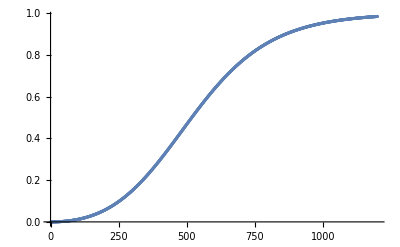

```mathematica
ListPlot[Flatten[list2],PlotRange->All]
```